# Frequency Domain Approach

Authors: Jaime Redondo-Yuste & Alejandro Cardenas-Avendaño
Auxiliary notebook related to Section III in 2502.18643

```mathematica
Quit[]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/jaimeredondoyuste/Documents/Projects/NonlinearKG/mma/good

## 0. Auxiliary stuff

```mathematica
ACoef[α_,rP_]:=rP^2(4-α^2);
BCoef[α_,rP_]:=(2+α)^2/rP^2;
pars[α_,rP_,L_]:={A->ACoef[α,rP], B-> BCoef[α,rP], l->L};
f[x_]:=1-(8 x^2)/(A+ B x^4);
$Assumptions={A>0, B>0, l>=0,x>0, ω!=0, Im[ω]!=0};
V = f[x](l(l+1)/x^2-f'[x]/x); 
ToFunction[expr_Rule]:=expr/.Rule[a_[t_],e_]:>Rule[a,Function[t,e]];
Lyapunov[α_,rP_] := 1/Sqrt[f[rP]^2(2/rP^2-f''[x]/f[rP])]/.x->rP/.pars[α,rP,l];
```

```mathematica
{$rp,$α}={rp, α} /. FindRoot[{
ACoef[α,rp]==8*(0.026`100),
BCoef[α,rp]==8*(11.20`100)
},
{{rp,0.20},{α,2}},
PrecisionGoal->80,
WorkingPrecision->80
]
```

{0.22882454596125273858332542947646668389812233392967270118294941728634585425185502,0.16599083238130595807539416982785379819592425204251535452399172201174597417930994}

## 1. Boundary conditions

```mathematica
ϕINdex[i_]:=Subscript[ϕIN, i];
ϕOUTdex[i_]:=Subscript[ϕOUT, i];
```

Choose order of the expansion. Recommended at least ~10

```mathematica
meH = 12;
meOUT=12;
```

#### 1.1. Horizon BCs

First, let us absorb the leading order piece

```mathematica
eqIN = f[x]^2 ϕH''[x] +f'[x]f[x]ϕH'[x]+ (ω^2-V)ϕH[x];
ϕH[x_]:=x^(l+1)ϕIN[x];
(eqIN==0//Simplify);
%[[1]]-%[[2]]
```

1/((A+B x^4)^3)x^(-1+l) ((-((A-8 x^2+B x^4) (-32 B x^6+16 x^2 (A+B x^4)+l (1+l) (A+B x^4)^2))+x^2 (A+B x^4)^3 ω^2) ϕIN[x]+16 x^2 (-A+B x^4) (A-8 x^2+B x^4) ((1+l) ϕIN[x]+x ϕIN'[x])+(A+B x^4) (A-8 x^2+B x^4)^2 (l (1+l) ϕIN[x]+x (2 (1+l) ϕIN'[x]+x ϕIN''[x])))

Now we expand in series

```mathematica
eqH = (-((A-2 x^2+B x^4) (-8 B x^6+4 x^2 (A+B x^4)+l (1+l) (A+B x^4)^2))+x^2 (A+B x^4)^3 ω^2) ϕIN[x]+4 x^2 (-A+B x^4) (A-2 x^2+B x^4) ((1+l) ϕIN[x]+x ϕIN'[x])+(A+B x^4) (A-2 x^2+B x^4)^2 (l (1+l) ϕIN[x]+x (2 (1+l) ϕIN'[x]+x ϕIN''[x]));
ϕIN[x_]:= Sum[Subscript[ϕIN, i](x)^i,{i,0,meH}]+O[x,0]^(meH+1);
```

```mathematica
zeroexp={};
Monitor[Do[
aux=(Series[eqH,{x,0,i}]/.zeroexp//Simplify);
aux1=Simplify[(aux//Normal)==0];
aux2 = CoefficientList[aux1[[1]]-aux1[[2]], ϕINdex[i]];
aux3 =ToFunction/@ {ϕINdex[i]->Simplify[ (-aux2[[1]])/aux2[[2]]]};
zeroexp=AppendTo[zeroexp,aux3[[1]]];,
{i,1,meH}
],i]
```

And we grab this as a function

```mathematica
ϕ$in[R_,pars_,ϕ0_:1]:=SetPrecision[(x^(l+1)ϕIN[x]/.zeroexp/.pars//Normal//Simplify)/.x->R/.Subscript[ϕIN, 0]->ϕ0,100];
ψ$in[R_,pars_,ϕ0_:1]:=SetPrecision[(D[x^(l+1)ϕIN[x],x]/.zeroexp/.pars//Normal//Simplify)/.x->R/.Subscript[ϕIN, 0]->ϕ0,100];
```

#### 1.2. Infinity BCs

The first step of the derivation is easier done by hand, since the natural coordinate there is r_* and not r...

```mathematica
eqINF =ϕOUT''[x] f[x]^2+ϕOUT'[x]( f'[x]f[x]+2 I ω f[x])-V ϕOUT[x];
ϕOUT[x_]:= Sum[Subscript[ϕOUT, i]/x^i,{i,0,meOUT}]+O[x,∞]^(meOUT+1);
```

```mathematica
infexp={};
Monitor[Do[
aux=(Series[eqINF,{x,∞,i+1}]/.infexp//Simplify);
aux1=Simplify[(aux//Normal)==0];
aux2 = CoefficientList[aux1[[1]]-aux1[[2]], ϕOUTdex[i]];
aux3 =ToFunction/@ {ϕOUTdex[i]->Simplify[ (-aux2[[1]])/aux2[[2]]]};
infexp=AppendTo[infexp,aux3[[1]]];,
{i,1,meOUT}
],i]
```

We need to integrate r_* as a function of r now. After testing, it is actually more efficient to integrate numerically

```mathematica
rsNum[x_?NumericQ,pars_]:=Module[
{sol,auxFun,res},
sol=First@NDSolve[{auxFun'[r]==1/f[r]/.pars, auxFun[10^-5]==10^-5},auxFun[r],{r,10^-5,x}];
res=auxFun[r]/.sol ;
res/.r->x
]
```

```mathematica
ϕ$out[R_?NumericQ,pars_,ϕ0_:1]:=SetPrecision[(Exp[I ω rsNum[R,pars]]ϕOUT[x]/.infexp/.pars//Normal//Simplify)/.x->R/.Subscript[ϕOUT, 0]->ϕ0,100];
ψ$out[R_?NumericQ,pars_,ϕ0_:1]:=SetPrecision[(Exp[I ω rsNum[R,pars]](D[ϕOUT[x],x]+I ω/f[R] ϕOUT[x])/.infexp/.pars//Normal//Simplify)/.x->R/.Subscript[ϕOUT, 0]->ϕ0,100];
```

## 2. Construct IN and OUT solutions & Wronskian

```mathematica
solIN[r_?NumericQ,Ω2_?NumericQ,pars_,rmin_:10^-3,prec_:18]:=Module[
{Ω,ruleP, BCS, EQ, sol,rt},
Ω=SetPrecision[Ω2, 100];
ruleP={AccuracyGoal->prec,PrecisionGoal->prec,WorkingPrecision-> 2*prec+4,Method->"StiffnessSwitching"};
BCS = {ϕ[rmin]==ϕ$in[rmin,pars], ϕ'[rmin]==ψ$in[rmin,pars]}/.ω->Ω;
EQ = {(f[x]^2 ϕ''[x]+f'[x]f[x]ϕ'[x]+ (Ω^2-V)ϕ[x])==0}/.pars;
sol= (ϕ[x]/.First@NDSolve[Union[EQ,BCS],ϕ,{x,rmin,r},ruleP]);
rt[y_]:=sol/.x->y;
Return[rt]
];

solOUT[r_?NumericQ,Ω2_?NumericQ,pars_,rmax_:100,prec_:18]:=Module[
{Ω,ruleP, BCS, EQ, sol,rt},
Ω=SetPrecision[Ω2, 100];
ruleP={AccuracyGoal->prec,PrecisionGoal->prec,WorkingPrecision-> 2*prec+4,Method->"StiffnessSwitching"};
BCS = {ϕ[rmax]==ϕ$out[rmax,pars], ϕ'[rmax]==ψ$out[rmax,pars]}/.ω->Ω;
EQ = {(f[x]^2 ϕ''[x]+f'[x]f[x]ϕ'[x]+ (Ω^2-V)ϕ[x])==0}/.pars;
sol= (ϕ[x]/.First@NDSolve[Union[EQ,BCS],ϕ,{x,rmax,r},ruleP]);
rt[y_]:=sol/.x->y;
Return[rt]
];

WR[r_?NumericQ,Ω2_?NumericQ,pars_,rmin_:10^-3,rmax_:100]:=Module[
{ϕIN, ϕOUT, ψIN, ψOUT},
ϕIN= solIN[r,Ω2,pars,rmin];
ψIN[y_?NumericQ]:=D[ϕIN[x],x]/.x->y;
ϕOUT= solOUT[r,Ω2,pars,rmax];
ψOUT[y_?NumericQ]:=D[ϕOUT[x],x]/.x->y;
Return[ϕIN[r]ψOUT[r]-ϕOUT[r]ψIN[r]]
]
```

Check: Wr = Wr(R) f(R) / f(x) for some value of R

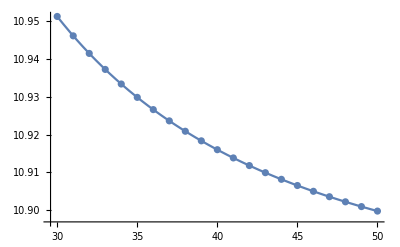

```mathematica
wr=Monitor[Table[{xx,Abs@WR[xx,1,pars[2/10,2,2]]},{xx,30,50,1}],xx];
p1=ListPlot[Abs@wr,PlotRange->All];
p2=Plot[wr[[1,2]]f[30]/f[x]/.pars[2/10,2,2],{x,30,50}];
Show[p1,p2]
```

## 3. Direct Integration method

```mathematica
INT[Ω2_?NumericQ,pars_,rmin_?NumericQ,rmax_?NumericQ,r1_?NumericQ,prec_:18] := Module[
{Ω,ruleP,BCS,EQS,sol0,sol∞ , ϕ0,ϕ∞,ψ0,ψ∞,scaling, Δψ,ψn},
Ω=SetPrecision[Ω2,100];
ruleP={AccuracyGoal->prec,PrecisionGoal->prec,WorkingPrecision-> 2*prec+4,Method->"StiffnessSwitching"};

(*Integrate from r=0*)

BCS = {ϕ[rmin]==ϕ$in[rmin,pars], ϕ'[rmin]==ψ$in[rmin,pars]}/.ω->Ω;
EQS = {(f[x]^2 ϕ''[x]+f'[x]f[x]ϕ'[x]+ (Ω^2-V)ϕ[x])==0}/.pars;

sol0  = First@NDSolve[Union[EQS,BCS],ϕ,{x,rmin,r1},ruleP];
ϕ0=ϕ[x]/.sol0;
ψ0=D[ϕ0,x];

(*Integrate from r=∞*)

BCS = {ϕ[rmax]==ϕ$out[rmax,pars], ϕ'[rmax]==ψ$out[rmax,pars]}/.ω->Ω;

sol∞ = First@NDSolve[Union[EQS,BCS],ϕ,{x,rmax,r1},ruleP];
ϕ∞=ϕ[x]/.sol∞;
ψ∞=D[ϕ∞,x];

scaling=ϕ0/(ϕ∞)/.x->r1;
Δψ = (ψ0-scaling ψ∞)/ψ0/.x->r1;
ψn[z_]:=Piecewise[{{ϕ0/.x->z,z<r1},{scaling ϕ∞/.x->z,z≥r1}}];
{Δψ,ψn}
]

QNM[ωGuess_?NumericQ, pars_,prec_:18, rmin_:10^-3, rmax_:1000, rmatch_:6]:=Module[
{faux, freq,check,mode2,mode},
faux[y_?NumericQ]:=INT[y,pars,rmin,rmax,rmatch,prec][[1]];
freq=y/.FindRoot[faux[y]==0,{y,ωGuess}][[1]];
{check,mode2}=INT[freq,pars,rmin,rmax,rmatch,prec];
mode=solIN[rmax,freq,pars,rmin,prec];
{freq,Abs[check],mode}
];
```

## 4. WKB Approximation

#### 4.1. Main functions

```mathematica
𝒬[ω_,α_,rp_,l_,x_]:=ω^2-V /. pars[α,rp,l];
LRmin[α_,rp_,l_]:=x/.Quiet@FindMaximum[V /. pars[α,rp,l], {x,3/2*rp}][[2]];
LRplu[α_,rp_,l_]:=x/.Quiet@FindMinimum[V /. pars[α,rp,l], {x,rp}][[2]];
Vmin[α_,rp_,l_]:=V /. pars[α,rp,l] /. x->LRplu[α,rp,l];
Vmax[α_,rp_,l_]:= V /. pars[α,rp,l] /. x->LRmin[α,rp,l];
```

Automatically use as guess the average value between Vmin and Vmax.

```mathematica
MaxOvertone[α_,rp_,l_] :=Module[
{LRp,ra,LRm,w,int},
LRp=LRmin[α,rp,l];
LRm=LRplu[α,rp,l];
w = Sqrt[V/.pars[α,rp,l]/.x-> LRp];
ra =  x/.FindRoot[𝒬[w,α,rp,l,x]==0, {x, rp/2}];
int=1/π NIntegrate[Sqrt[𝒬[w,α,rp,l,x]]/(f[x]/.pars[α,rp,l]),{x,ra,LRp}];
Return[Floor[int-1/2]]
]
```

```mathematica
On[Assert];
WKBINT[ωGuess_?NumericQ, α_,rp_,l_,n_] := Module[
{ra, rb,LRm},
Assert[Vmin[α,rp,l]<ωGuess^2<Vmax[α,rp,l]];
LRm=LRplu[α,rp,l];
ra = x/.FindRoot[𝒬[ωGuess,α,rp,l,x]==0, {x, rp/2}];
rb = x/.FindRoot[𝒬[ωGuess,α,rp,l,x]==0, {x, 1.1LRm}];
NIntegrate[Sqrt[𝒬[ωGuess,α,rp,l,x]]/(f[x]/.pars[α,rp,l]),{x,ra,rb}]-π(n+1/2)
]

WKBRe[ωGuess_?NumericQ,α_,rp_,l_,n_]:=Module[
{aux,x0,x1},
aux[ω_] := WKBINT[ω, α, rp, l, n];
x0=(1+10^-3)Sqrt[Vmin[α,rp,l]];
x1=(1-10^-3)Sqrt[Vmax[α,rp,l]];
ω/.FindRoot[aux[ω],{ω,ωGuess,x0,x1}][[1]]
]

χ[r_?NumericQ,ωRe_,α_,rp_,l_]:=Module[
{ra},
ra=x/.FindRoot[𝒬[ωRe,α,rp,l,x]==0, {x, rp/2}];
-π/4+NIntegrate[Sqrt[𝒬[ωRe,α,rp,l,x]]/(f[x]/.pars[α,rp,l]),{x,ra,r}]
];

gamma[ωRe_,α_,rp_,l_]:=Module[
{LRm,ra,rb,chi},
LRm=LRplu[α,rp,l];
ra = x/.FindRoot[𝒬[ωRe,α,rp,l,x]==0, {x, rp/2}];
rb = x/.FindRoot[𝒬[ωRe,α,rp,l,x]==0, {x, 1.1 LRm}];
chi[x_?NumericQ]:=χ[x,ωRe,α,rp,l];
NIntegrate[Cos[chi[x]]^2/(f[x] Sqrt[𝒬[ωRe,α,rp,l,x]]/.pars[α,rp,l]),{x,ra,rb}]
];

Γamma[ωRe_,α_,rp_,l_]:=Module[
{LRm,LRp,rb,rc},
LRm=LRplu[α,rp,l];
LRp=LRmin[α,rp,l];
rc = x/.FindRoot[𝒬[ωRe,α,rp,l,x]==0, {x, 1.1LRp}];
rb = x/.FindRoot[𝒬[ωRe,α,rp,l,x]==0, {x, 1.1 LRm}];
2*NIntegrate[Sqrt[-𝒬[ωRe,α,rp,l,x]]/(f[x]/.pars[α,rp,l]),{x,rb,rc}]
];

WKBIm[ωRe_,α_,rp_,l_]:=-Exp[-Γamma[ωRe,α,rp,l]]/(4 ωRe gamma[ωRe,α,rp,l]);

WKB[α_,rp_,l_,n_,ωGuess_:0]:=Module[
{guess,ωRe,ωIm},
If[ωGuess==0,
guess=Sqrt[1/2(Vmin[α,rp,l]+Vmax[α,rp,l])];,
guess=ωGuess;];
ωRe=WKBRe[guess,α,rp,l,n];
ωIm=WKBIm[ωRe,α,rp,l];
ωRe+ωIm*I
]
```

#### 4.2. Example: compute QNM freqs

```mathematica
QNMFreqs=Monitor[Table[
ω=$rp*WKB[$α,$rp,l,0];
{Re@ω,-1/Im@ω},
{l,4,12}
],l];
```

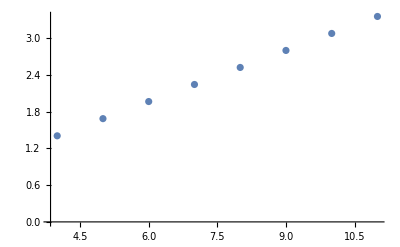

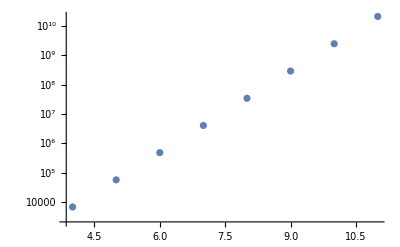

```mathematica
ListPlot[Table[{i+3,Re@QNMFreqs[[i]][[1]]},{i,1,12-4}]]
ListLogPlot[Table[{i+3,Re@QNMFreqs[[i]][[2]]},{i,1,12-4}]]
```

## 5. Breit-Wigner approach

#### 5.1. Main functions

```mathematica
BreitWigner[Ω_,pars_,rmax_:25,prec_:18]:= Module[
{sol,ns, a,b},
sol=solIN[rmax,Ω,pars,10^-3,prec];
ns = First@NSolve[{
Re[sol[rmax]]== a Cos[Ω rmax] + b Sin[Ω rmax],
Re[sol'[rmax]]== -Ω a Sin[Ω rmax] + b Ω Cos[Ω rmax]
},
{a,b}];
a = a/.ns;
b = b/.ns;
a^2+b^2
];
```

```mathematica
BWFreq[Ω2_,par_,prec_:18,search_:10^-6,rmax_:25]:=Module[
{data,ΩGuess,int,ωR1,data2,nlm,ωR,ωI},
ΩGuess=SetPrecision[Ω2,100];(*First broad search*)
data=Table[{Ω,BreitWigner[Ω,par,rmax,prec]},{Ω,(1-10^-2)  ΩGuess,(1+10^-2)  ΩGuess,10^-3  ΩGuess}];
int=Interpolation[data];
ωR1=Re[x]/.First@Quiet@FindRoot[int'[x]==0, {x, ΩGuess}];
data2 =Table[{Ω,Abs@BreitWigner[Ω,par,rmax,prec]},{Ω,(1-search) ωR1,(1+search)ωR1,search/10 ωR1}];
nlm=LinearModelFit[data2,{x,x^2},x];
ωR=Re[x]/.First@Quiet@FindRoot[nlm'[x]==0, {x, ωR1},AccuracyGoal->6];
ωI=Re[Sqrt[(2 nlm[ωR])/nlm''[ωR]]];
Return[ωR-I ωI]
];
```

#### 5.2. Example (l=4)

```mathematica
bw4 = Monitor[Table[{Ω, BreitWigner[Ω/($rp),pars[$α,$rp,4]]},{Ω,1,2,2/100}],N[Ω]];
```

We find the kinks close to the frequencies computed with WKB

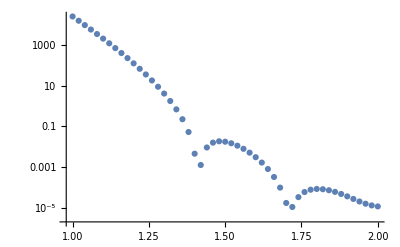

```mathematica
ListLogPlot[bw4]
```

#### 5.3. Point-wise comparison

Compare BW Vs WKB

```mathematica
ω40$WKB=WKB[$α,$rp,4,0]
ω40$BW=BWFreq[Re@ω40$WKB,pars[$α,$rp,4]]
```

6.14448-0.000627095 ⅈ

6.1704-0.000616851 ⅈ

## 6. Check against direct integration

#### 6.1. Check frequency for l=4

```mathematica
guess=WKB[$α,$rp,4,0];
{ω40,err,ψ40}=QNM[Re@guess,pars[$α,$rp,4],Max[18, 3*(4+1)],10^-3, (200*$rp)/Sqrt[4],$rp];
```

```mathematica
ω40 * $rp
QNMFreqs[[1,1]]-I/QNMFreqs[[1,2]]
ω40$BW*$rp
```

1.41186-0.000158026 ⅈ

1.40601-0.000143495 ⅈ

1.41194-0.000141151 ⅈ

#### 6.2. Radial Structure

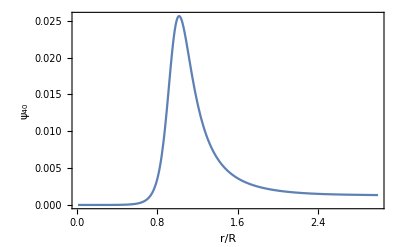

```mathematica
Plot[Abs@ψ40[r*$rp],{r,0.01,3},PlotRange->All,Frame->True,FrameLabel->{"r/R","ψ_40"}]
```